L = 5

nParticles = 3

J Matrix:

(0 | J01 | J02 | J03
J01 | 0 | J12 | J13
J02 | J12 | 0 | J23
J03 | J13 | J23 | 0)

Total configurations: 60

First few: {{1,2,3,0,0},{1,3,2,0,0},{2,1,3,0,0},{2,3,1,0,0},{3,1,2,0,0}}

Transition matrix row sums: {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Transition matrix:

Showing 5x5 block:

(1/8 (-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), True}}])-2 (-4+(Piecewise[{{1, J23≤0}, {ⅇ^(-J23 β), True}}])+(Piecewise[{{1, J12≤J13}, {ⅇ^((-J12+J13) β), J12>J13}, {0, True}}])+(Piecewise[{{1, J23≤J13}, {ⅇ^((J13-J23) β), J23>J13}, {0, True}}]))) | 1/4 (Piecewise[{{1, J12≤J13}, {ⅇ^((-J12+J13) β), J12>J13}, {0, True}}]) | 1/4 (Piecewise[{{1, J23≤J13}, {ⅇ^((J13-J23) β), J23>J13}, {0, True}}]) | 0 | 0
1/4 (Piecewise[{{1, J13≤J12}, {ⅇ^((J12-J13) β), J13>J12}, {0, True}}]) | 1/8 (-(Piecewise[{{1, J13≤0}, {ⅇ^(-J13 β), True}}])-2 (-4+(Piecewise[{{1, J23≤0}, {ⅇ^(-J23 β), True}}])+(Piecewise[{{1, J13≤J12}, {ⅇ^((J12-J13) β), J13>J12}, {0, True}}])+(Piecewise[{{1, J23≤J12}, {ⅇ^((J12-J23) β), J23>J12}, {0, True}}]))) | 0 | 0 | 1/4 (Piecewise[{{1, J23≤J12}, {ⅇ^((J12-J23) β), J23>J12}, {0, True}}])
1/4 (Piecewise[{{1, J13≤J23}, {ⅇ^((-J13+J23) β), J13>J23}, {0, True}}]) | 0 | 1/8 (-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), True}}])-2 (-4+(Piecewise[{{1, J13≤0}, {ⅇ^(-J13 β), True}}])+(Piecewise[{{1, J12≤J23}, {ⅇ^((-J12+J23) β), J12>J23}, {0, True}}])+(Piecewise[{{1, J13≤J23}, {ⅇ^((-J13+J23) β), J13>J23}, {0, True}}]))) | 1/4 (Piecewise[{{1, J12≤J23}, {ⅇ^((-J12+J23) β), J12>J23}, {0, True}}]) | 0
0 | 0 | 1/4 (Piecewise[{{1, J23≤J12}, {ⅇ^((J12-J23) β), J23>J12}, {0, True}}]) | 1/8 (-2 (Piecewise[{{1, J13≤0}, {ⅇ^(-J13 β), True}}])-(Piecewise[{{1, J23≤0}, {ⅇ^(-J23 β), True}}])-2 (-4+(Piecewise[{{1, J13≤J12}, {ⅇ^((J12-J13) β), J13>J12}, {0, True}}])+(Piecewise[{{1, J23≤J12}, {ⅇ^((J12-J23) β), J23>J12}, {0, True}}]))) | 0
0 | 1/4 (Piecewise[{{1, J12≤J23}, {ⅇ^((-J12+J23) β), J12>J23}, {0, True}}]) | 0 | 0 | 1/8 (-2 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), True}}])-(Piecewise[{{1, J13≤0}, {ⅇ^(-J13 β), True}}])-2 (-4+(Piecewise[{{1, J12≤J23}, {ⅇ^((-J12+J23) β), J12>J23}, {0, True}}])+(Piecewise[{{1, J13≤J23}, {ⅇ^((-J13+J23) β), J13>J23}, {0, True}}]))))

Detailed balance: SATISFIED

Decision tree for first state:

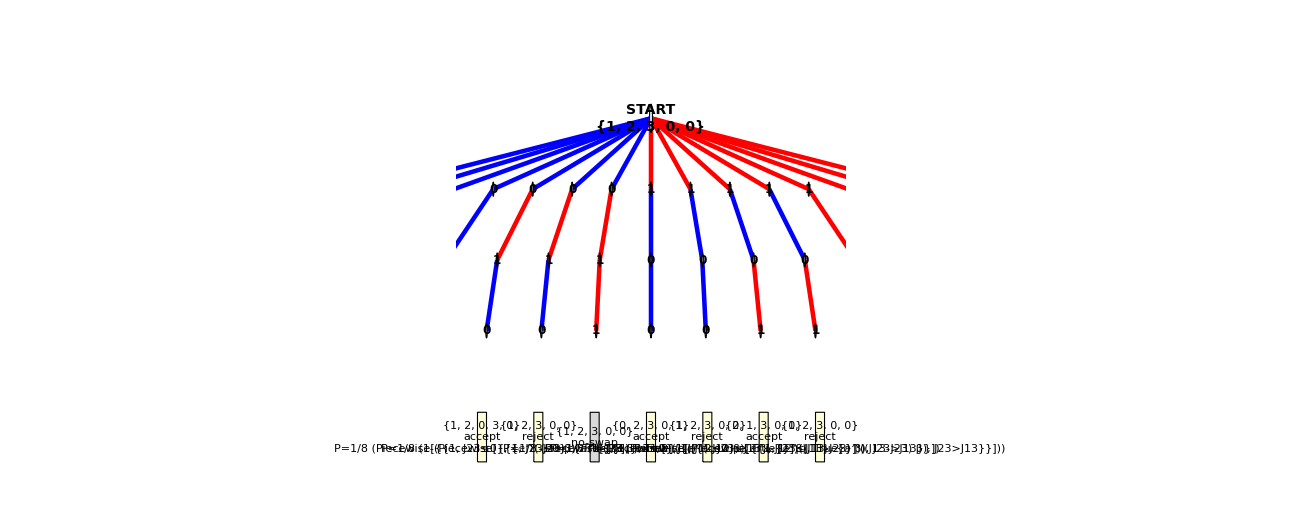

Decision tree for second state:

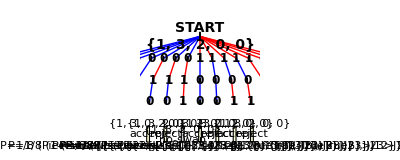

```mathematica
ClearAll["Global`*"]

(* =========================================*)
(*SETUP*)
(* =========================================*)

L=5;
nParticles=3;
β=Symbol["β"];

Print["L = ",L];
Print["nParticles = ",nParticles];

(* =========================================*)
(*SYMBOLIC J MATRIX*)
(* =========================================*)

GenerateSymbolicJ[n_]:=Module[{J=Table[0,{n+1},{n+1}]},Do[If[i<j,J[[i+1,j+1]]=Symbol["J"<>ToString[i]<>ToString[j]];
J[[j+1,i+1]]=J[[i+1,j+1]]],{i,0,n},{j,0,n}];
J]

JMatrix=GenerateSymbolicJ[nParticles];

Print["J Matrix:"];
Print[JMatrix//MatrixForm];

(* =========================================*)
(*ENERGY*)
(* =========================================*)

SymbolicEnergy[lattice_]:=Module[{E=0,i,j},Do[j=If[i==Length[lattice],1,i+1];
If[lattice[[i]]!=0&&lattice[[j]]!=0,E-=JMatrix[[lattice[[i]]+1,lattice[[j]]+1]]],{i,Length[lattice]}];
E]

(* =========================================*)
(*CONFIGURATIONS*)
(* =========================================*)

GenerateAllConfigs[L_,n_]:=Flatten[Table[Module[{lat=ConstantArray[0,L]},Do[lat[[pos[[i]]]]=perm[[i]],{i,n}];
lat],{pos,Subsets[Range[L],{n}]},{perm,Permutations[Range[n]]}],1]

states=GenerateAllConfigs[L,nParticles];
Print["Total configurations: ",Length[states]];
Print["First few: ",Take[states,Min[5,Length[states]]]];

(* =========================================*)
(*TREE RANDOMNESS*)
(* =========================================*)

$BinaryChoices={};
$BinaryIndex=1;

BinaryBit[]:=Module[{b},b=$BinaryChoices[[$BinaryIndex]];
$BinaryIndex++;
b]

DecodeInteger[nBits_]:=FromDigits[Table[BinaryBit[],{nBits}],2]



(* =========================================*)
(*KAWASAKI MOVE—normalized probabilities*)
(* =========================================*)

KawasakiMoveFromBits[lattice_]:=Module[{Lsize,nBits,raw,i,j,new,ΔE,p,siteProb},Lsize=Length[lattice];
(*siteProb=1/Lsize*) (*previous, but isn't normalised, probably not a problem though*)
nBits=Ceiling[Log2[Lsize]];
siteProb=1/(2^nBits);  (*Probability of this specific bit pattern*)

raw=DecodeInteger[nBits];
i=1+Mod[raw,Lsize];
j=If[i==Lsize,1,i+1];
If[lattice[[i]]==lattice[[j]],Return[{"no-swap",lattice,siteProb}]];
new=lattice;
new[[{i,j}]]=lattice[[{j,i}]];
ΔE=SymbolicEnergy[new]-SymbolicEnergy[lattice];
p=Piecewise[{{1,ΔE<=0},{Exp[-β ΔE],ΔE>0}}];
{{"accept",new,siteProb*p},{"reject",lattice,siteProb*(1-p)}}]





(* =========================================*)
(*TREE ENUMERATION*)
(* =========================================*)

EnumerateTree[lattice_]:=Module[{nBitsForSite,allBits,results},nBitsForSite=Ceiling[Log2[Length[lattice]]];
allBits=Tuples[{0,1},nBitsForSite];
results=Flatten[Table[($BinaryChoices=bits;
$BinaryIndex=1;
With[{out=KawasakiMoveFromBits[lattice]},If[First[out]==="no-swap",{{bits,"no-swap",out[[2]],out[[3]]}},{{bits,"accept",out[[1,2]],out[[1,3]]},{bits,"reject",out[[2,2]],out[[2,3]]}}]]),{bits,allBits}],1];
results]

(* =========================================*)
(*TREE VISUALIZATION—BIG,SCROLLABLE*)
(* =========================================*)

VisualizeDecisionTree[initialState_]:=Module[{tree,nBitsForSite,nBitsTotal,yLevels,xSpacing,nodeRadius,rootX,rootY,pathGraphics,baseXPositions,imageWidth,plotRangeX,Lsize,rootGraphics},tree=EnumerateTree[initialState];
Lsize=Length[initialState];
nBitsForSite=Ceiling[Log2[Lsize]];
nBitsTotal=nBitsForSite;
(*Use a wide layout for scrolling*)imageWidth=Max[1800,Length[tree]*60];
plotRangeX=Max[50,Length[tree]*3];
yLevels=Range[nBitsTotal,0,-1]*2;
xSpacing=Max[20,Length[tree]*1.5];
nodeRadius=0.2;
rootX=0;
rootY=yLevels[[1]];
baseXPositions=Table[(i-(Length[tree]+1)/2)*(xSpacing/1.5),{i,Length[tree]}];
pathGraphics=Table[Module[{path,pathType,finalState,probability,currentX,currentY,lineGraphics,circleGraphics,labelGraphics,bit,level,nextX,nextY,edgeColor,leafY,leafX,leafColor,leafText,treeEntry},treeEntry=tree[[i]];
path=Part[treeEntry,1];
pathType=Part[treeEntry,2];
finalState=Part[treeEntry,3];
probability=Part[treeEntry,4];
currentX=rootX;
currentY=rootY;
lineGraphics={};
circleGraphics={};
labelGraphics={};
Do[bit=path[[level]];
nextX=baseXPositions[[i]]+(currentX-baseXPositions[[i]])*0.3;
nextY=yLevels[[level+1]];
edgeColor=Which[bit==0,Blue,bit==1,Red,True,Black];
AppendTo[lineGraphics,{edgeColor,Thickness[0.0025],Arrowheads[0],Arrow[{{currentX,currentY},{nextX,nextY}}]}];
AppendTo[circleGraphics,{White,EdgeForm[{Black,Thin}],Disk[{nextX,nextY},nodeRadius]}];
AppendTo[labelGraphics,Text[Style[bit,Bold,12],{nextX,nextY}]];
currentX=nextX;
currentY=nextY;,{level,Length[path]}];
leafY=-3;
leafX=baseXPositions[[i]];
{leafColor,leafText}=Which[pathType=="no-swap",{LightGray,Column[{Style[ToString[finalState],Gray,12],Style["no-swap",Gray,10]},Center,Spacings->0.1]},pathType=="accept",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["accept",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]},pathType=="reject",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["reject",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]}];
AppendTo[circleGraphics,{leafColor,EdgeForm[{Black,Thin}],Rectangle[{leafX-1.2,leafY-0.7},{leafX+1.2,leafY+0.7}]}];
AppendTo[labelGraphics,Text[leafText,{leafX,leafY}]];
{lineGraphics,circleGraphics,labelGraphics}],{i,Length[tree]}];
rootGraphics={{LightBlue,EdgeForm[{Black,Thick}],Disk[{rootX,rootY},nodeRadius*2]},Text[Style["START\n"<>ToString[initialState],Bold,14],{rootX,rootY}]};
(*Wrap the tree in a scrollable pane*)Pane[Graphics[{pathGraphics,rootGraphics},PlotRange->{{-plotRangeX,plotRangeX},{-4,yLevels[[1]]+2}},AspectRatio->0.4,Background->White],{1800,600},Scrollbars->True]]

(* =========================================*)
(*TRANSITION MATRIX*)
(* =========================================*)

EnumerateTransitions[lattice_]:=Module[{tree},tree=EnumerateTree[lattice];
Merge[Table[{lattice,tree[[i,3]]}->tree[[i,4]],{i,Length[tree]}],Total]]

BuildTransitionMatrix[states_]:=Module[{n,idx,M,trans},n=Length[states];
idx=AssociationThread[states->Range[n]];
M=ConstantArray[0,{n,n}];
Do[trans=EnumerateTransitions[s];
KeyValueMap[(M[[idx[#1[[1]]],idx[#1[[2]]]]]=Simplify[#2])&,trans],{s,states}];
M]

transitionMatrix=BuildTransitionMatrix[states];

Print["\nTransition matrix row sums: ",Simplify[Total[transitionMatrix,{2}]]];
Print["Transition matrix:"];
If[Length[states]<=10,Print[transitionMatrix//MatrixForm],Print["Showing 5x5 block:"];
Print[Take[transitionMatrix,{1,5},{1,5}]//MatrixForm]];

(* =========================================*)(*DETAILED BALANCE CHECK—fixed FullSimplify logic*)(* =========================================*)theoreticalDist=Table[Exp[-β*SymbolicEnergy[states[[i]]]],{i,Length[states]}];
Z=Total[theoreticalDist];
theoreticalDist=theoreticalDist/Z;

violations=Flatten[Table[theoreticalDist[[i]]*transitionMatrix[[i,j]]-theoreticalDist[[j]]*transitionMatrix[[j,i]],{i,Length[states]},{j,i+1,Length[states]}]];

(*Remove literal zeros*)
nonZero=DeleteCases[violations,0];

(*Attempt simplification if necessary*)
If[Length[nonZero]>0,Module[{fsTest},fsTest=Quiet[Check[FullSimplify[nonZero[[1]]],"FAIL"]];
(*Use PossibleZeroQ instead of===0*)If[fsTest=!="FAIL"&&PossibleZeroQ[fsTest],(*FullSimplify all violations in parallel*)nonZero=ParallelMap[FullSimplify,nonZero];]]];

Print["\nDetailed balance: ",If[Length[Select[nonZero,!PossibleZeroQ[#]&]]==0,"SATISFIED",ToString[Length[Select[nonZero,!PossibleZeroQ[#]&]]]<>" violations"]];


(* =========================================*)
(*VISUALIZE TREES FOR FIRST TWO STATES*)
(* =========================================*)

Print["\nDecision tree for first state:"];
tree1=VisualizeDecisionTree[states[[1]]];
Print[tree1];

If[Length[states]>1,Print["\nDecision tree for second state:"];
tree2=VisualizeDecisionTree[states[[2]]];
Print[tree2];];
```

```mathematica
(* =========================================*)(*NUMERICAL SIMULATION*)(* =========================================*)(*Generate random symmetric J matrix*)GenerateRandomJMatrix[n_]:=Module[{J},J=Table[0,{n+1},{n+1}];
Do[If[i<j,J[[i+1,j+1]]=RandomReal[{-1,1}];
J[[j+1,i+1]]=J[[i+1,j+1]]],{i,0,n},{j,0,n}];
J]

(*Set numerical values*)
SeedRandom[1]; (*for reproducibility of J matrix*)
JMatrixNum=GenerateRandomJMatrix[nParticles];
βNum=1.0;

Print["Numerical J Matrix:"];
Print[JMatrixNum//MatrixForm];

(*Define numerical energy function*)
NumericalEnergy[lattice_]:=Module[{E=0,i,j},Do[j=If[i==Length[lattice],1,i+1];
If[lattice[[i]]!=0&&lattice[[j]]!=0,E-=JMatrixNum[[lattice[[i]]+1,lattice[[j]]+1]]],{i,Length[lattice]}];
E]

(*Replace symbolic J and β with numerical values for MCMC*)
JMatrix=JMatrixNum;
β=βNum;

(*Initial state*)
currentState=states[[1]];

(*Number of iterations*)
nSteps=500000;

(*Run simulation*)
SeedRandom[12];
trajectory=NestList[Function[lattice,Module[{nBits,bits,result},nBits=Ceiling[Log2[Length[lattice]]];
bits=RandomInteger[{0,1},nBits];
$BinaryChoices=bits;
$BinaryIndex=1;
result=KawasakiMoveFromBits[lattice];
If[First[result]==="no-swap",result[[2]],If[RandomReal[]<result[[1,3]],result[[1,2]],result[[2,2]]]]]],currentState,nSteps];

(*Print first few states*)
Print["First 10 states:"];
Print[Take[trajectory,10]];

(*Count state frequencies*)
stateCounts=Counts[trajectory];
Print["\nState frequencies:"];
Print[stateCounts//Normal];
```

Numerical J Matrix:

(0 | 0.634779 | -0.777161 | 0.579052
0.634779 | 0 | -0.624394 | -0.517278
-0.777161 | -0.624394 | 0 | -0.868522
0.579052 | -0.517278 | -0.868522 | 0)

First 10 states:

{{1,2,3,0,0},{1,2,3,0,0},{1,2,3,0,0},{1,2,3,0,0},{1,2,3,0,0},{1,2,3,0,0},{1,2,3,0,0},{1,2,3,0,0},{1,2,3,0,0},{1,2,3,0,0}}

State frequencies:

{{1,2,3,0,0}→4762,{1,3,2,0,0}→5284,{0,3,2,0,1}→9212,{3,0,2,0,1}→11622,{3,0,2,1,0}→10831,{0,3,2,1,0}→4928,{0,2,3,0,1}→8779,{2,0,3,0,1}→11116,{2,0,3,1,0}→13692,{2,0,1,3,0}→12962,{2,1,0,3,0}→11042,{0,1,0,3,2}→8599,{0,1,3,0,2}→13144,{0,3,1,0,2}→12697,{0,3,0,1,2}→11181,{0,3,0,2,1}→10680,{3,0,0,1,2}→4818,{2,3,0,1,0}→8902,{3,2,0,1,0}→8818,{0,2,0,1,3}→13660,{0,2,0,3,1}→12850,{2,3,0,0,1}→5092,{1,0,3,0,2}→11209,{1,0,0,3,2}→4267,{2,0,0,3,1}→6484,{0,0,2,3,1}→5623,{0,0,2,1,3}→7240,{1,0,2,3,0}→8524,{0,1,2,3,0}→4902,{1,2,0,3,0}→11680,{2,1,3,0,0}→6467,{1,3,0,2,0}→13295,{1,0,3,2,0}→9702,{3,1,0,2,0}→12790,{0,0,3,2,1}→5049,{3,0,0,2,1}→6428,{1,0,0,2,3}→5376,{1,0,2,0,3}→11298,{0,1,2,0,3}→11118,{2,1,0,0,3}→4608,{2,3,1,0,0}→5379,{0,0,3,1,2}→6450,{3,2,0,0,1}→5677,{3,0,1,2,0}→10818,{2,0,0,1,3}→5640,{0,2,3,1,0}→5776,{1,2,0,0,3}→6191,{3,1,2,0,0}→6667,{0,1,0,2,3}→9248,{3,0,1,0,2}→8655,{0,0,1,2,3}→5078,{0,0,1,3,2}→5332,{0,2,1,3,0}→7748,{0,1,3,2,0}→5543,{0,2,1,0,3}→11804,{3,2,1,0,0}→4854,{1,3,0,0,2}→7158,{0,3,1,2,0}→6572,{2,0,1,0,3}→9460,{3,1,0,0,2}→5220}

Observed counts: {4762,5284,6467,5379,6667,4854,11680,13295,11042,8902,12790,8818,6191,7158,4608,5092,5220,5677,8524,9702,12962,13692,10818,10831,11298,11209,9460,11116,8655,11622,5376,4267,5640,6484,4818,6428,4902,5543,7748,5776,6572,4928,11118,13144,11804,8779,12697,9212,9248,8599,13660,12850,11181,10680,5078,5332,7240,5623,6450,5049}

Total observations: 500001

============================================================

CORRELATION ANALYSIS

============================================================

Pearson correlation coefficient: 0.9884

(Perfect agreement = 1.0)

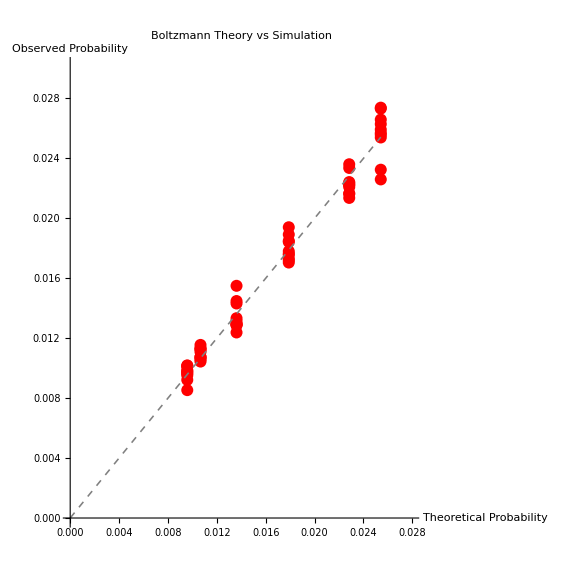

```mathematica
(* =========================================*)(*BOLTZMANN DISTRIBUTION ANALYSIS*)(* =========================================*)(*Step 1:Calculate energy for each state*)

energies=Table[NumericalEnergy[states[[i]]],{i,Length[states]}];

(*Step 2& 3:Calculate Boltzmann distribution*)boltzmannWeights=Exp[-βNum*energies];
partitionFunction=Total[boltzmannWeights];
theoreticalProbs=boltzmannWeights/partitionFunction;

(*Step 4:Get observed probabilities from simulation-FIXED*)observedCounts=Table[If[KeyExistsQ[stateCounts,states[[i]]],stateCounts[states[[i]]],0],{i,Length[states]}];

Print["Observed counts: ",observedCounts];
Print["Total observations: ",Total[observedCounts]];

(*Only calculate probabilities if we have observations*)
If[Total[observedCounts]>0,observedProbs=N[observedCounts/Total[observedCounts]],Print["ERROR: No observations found!"];
observedProbs=Table[0,{Length[states]}];];

(*Scatter plot:theory vs observed*)scatterPlot=ListPlot[Table[{theoreticalProbs[[i]],observedProbs[[i]]},{i,Length[states]}],PlotStyle->{Red,PointSize[0.015]},PlotLabel->"Boltzmann Theory vs Simulation",AxesLabel->{"Theoretical Probability","Observed Probability"},AspectRatio->1,Epilog->{Dashed,Gray,Thickness[0.002],Line[{{0,0},{Max[theoreticalProbs],Max[theoreticalProbs]}}]},ImageSize->Large,PlotRange->{{0,Max[theoreticalProbs]*1.1},{0,Max[observedProbs]*1.1}}];

(*Calculate correlation coefficient*)
correlation=Correlation[theoreticalProbs,observedProbs];

Print["\n"<>StringRepeat["=",60]];
Print["CORRELATION ANALYSIS"];
Print[StringRepeat["=",60]];
Print["Pearson correlation coefficient: ",NumberForm[correlation,{5,4}]];
Print["\n"];
Print[scatterPlot];
```